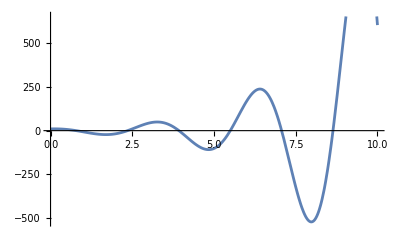

iter= 1  a= 8.  b= 9.  c=9.

iter= 2  a= 8.5  b= 9.  c=8.5

iter= 3  a= 8.5  b= 8.75  c=8.75

iter= 4  a= 8.625  b= 8.75  c=8.625

iter= 5  a= 8.625  b= 8.6875  c=8.6875

iter= 6  a= 8.625  b= 8.65625  c=8.65625

iter= 7  a= 8.625  b= 8.64063  c=8.64063

iter= 8  a= 8.63281  b= 8.64063  c=8.63281

iter= 9  a= 8.63672  b= 8.64063  c=8.63672

iter= 10  a= 8.63867  b= 8.64063  c=8.63867

```mathematica
Plot[10 E^(x/2)Cos[2x],{x,0.0,10.0}]
f[x_]=10 E^(x/2)Cos[2x];
a=8.0;
b=10.0;
c=N[(b+a)/2];
n=10;

For[i=1,i<=n, i++,
c=N[(b+a)/2];
 If[f[c]<0,
a=c,
b=c];

Print["iter= ",i,"  a= ", a, "  b= ",b, "  c=",c]

];
```